# Log analysis 20231001 - 20231029

## Title: CiNiiのログから見るユーザーアクセスグラフの計量分析

### 情報知識学会抄録

```mathematica
submittext=
"NIIでは、NIIが提供するResearch Data Cloudの各サービスのログを横断的に分析するための環境「統合ログ基盤」を整備してきた。本発表では特にCiNiiのログを対象にした当該基盤の機能を使ったログ分析結果の一部を紹介する。当該基盤の特徴は、(1)各アクセスログ（URL）に対してユーザーアクションを端的に示すラベル（ボキャブラリ）を付与する機能、(2)アクセスログを意味のある単位でまとめる（「リファラーグラフ」を生成する）機能をもつことであり、本研究ではこれらの機能を用いることにより個々のユーザーの行動をモデル化できる可能性を示す。";
```

```mathematica
StringLength[submittext]
```

276

## 対象期間：20231001 - 20231029

単日で行った分析結果のsaveを読み込み、4W分の分析を行う。

## コンセプト

アクセスログから分離したユーザーごとのアクセスグラフを一種のプロダクトとみなし、計量書誌学の観点から分析を行う。

用語：
アクセス：ログのアクセスURL
（アクセス）連鎖：リファラー -> アクセスURLとなる”エッジ”およびエッジが連なった”経路”または”グラフ” => グラフの場合はReferrer Graph[1] というらしい。
ユーザーアクセスグラフ：単一ユーザー（推定）によるアクセスのグラフ
ボキャブラリ：アクセスの性質・アクションを端的に表す単語

分析項目の候補：

ユーザーアクセスグラフの規模クラス内のメンバの分布（Zipを仮定）、1日/1週間/3ヶ月

クラスのメンバ数の分布が対象になるのでクラスを作る。（例：被引用が1件のクラス）

vertex数クラス

edge数クラス

リファラーと離脱次のURLのボキャブラリのペア

離脱時のURL（voc）/初回アクセスのドメイン

ボキャブラリ“detail”が付与される、タイムライン内のノードの位置

ボキャブラリ”detail”が付与されるノードの割合（高いほど効率的と仮定）

どのくらいのユーザーが”detail”まで確認しているか？

NIIサービス連携がどのくらいあるか？

滞留時間は精度がよくないので発表としては使わない？

ユーザーアクセスグラフの類型

プロパティ：voc出現（重み付き/重みなし）

プロパティ：vocによるアクセスグラフ（重み付き/重みなし）のスペクトル

非対称行列（隣接行列そのまま）のスペクトル

キルヒホフ行列のスペクトル（undirectedの場合重みなしとなる）

N次の連鎖

アクセスグラフの類型ごとのメンバー数がZip型分布に従うか？

アクセスグラフの類型をクラスタリングし類型間の関係を確認する

クラスタリング法は？使用する類型のプロパティは？

分析を組み合わせ、各々の類型がどのような行動パターンか説明可能か？

参照：

1. B. de la Ossa, A. Pont, J. Sahuquillo, J. A. Gil ; “Referrer graph: a low-cost web prediction algorithm” ; Proceedings of the 2010 ACM Symposium on Applied ComputingMarch 2010Pages 831–838 ; https://doi.org/10.1145/1774088.1774260

```mathematica
Grid[Import["/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/analysis_items.xlsx"][[1]],ItemSize->Full,Frame->All]
```

CiNiiのログから見るユーザーアクセスグラフの計量分析 |  |  |  |  |  |  |  |  |  |  |  |  | 
分析項目の整理 |  |  |  |  |  |  |  |  |  |  |  |  | 
 | 分析項目→ | ユーザーアクセスグラフの構成 | グラフの規模 | voc[detail]のグラフ内の位置 | リファラーと離脱時のアクセスURL(voc) | グラフのN次の連鎖パス | グラフに出現するvocのリスト | vocグラフスペクトル | 滞在/滞留時間 | 連携アクセス |  | [今後]キーワード分析 | [間に合うか？]グラフ使わないクロス集計
 | 目的→ | 分析の基本となるグラフを構成する | グラフの規模の分布を確認する | ・ユーザーがdetailページに辿り着いているか | ・各グラフにおける典型的な行動を捉える | ・各グラフにおける典型的な行動を捉える
・パスの規模の分布を確認する | ・グラフを類型化する
・グラフ類型のクラスタリング
・グラフ類型の規模の分布を確認する | ・グラフを類型化する
・グラフ類型のクラスタリング
・グラフ類型の規模の分布を確認する |  | ・ciと他基盤の連携グラフがどの程度あるか |  |  | 
 | コメント→ |  |  |  |  |  | 0/1出現を利用してクラスを決定
クラスを対象としてクラスタリング | グラフの固有値列を用いてクラスを決定
クラスを対象としてクラスタリング |  |  |  |  | ・リファラーと...
・組織と...
 | グラフタイプ↓/グラフから何を確認すれば良いか→ |  |  |  |  |  |  |  |  |  |  |  | 
 | Basic-graph
リファラー -> アクセスURLの連鎖による有向グラフ | グラフを構成 | - | - | - | - | - | - |  | - |  |  | 
 | voc-label-graph
上記のグラフのvertexにvocを付与したもの | Basic-graphからvoc-label-graphを構成 | ・Vertex
・Edge | ・グラフ内のvertexを最終アクセス時刻順に並べてdetailがどの位置にあるか | ・グラフ内の最初のリファラー
・グラフ内で最後にアクセスしたURL | ・最大連鎖長をグラフごとに取る
・1次（Vertex）
・2次（Edge）
・3次
・何次まで？ | ・重みつきvocリスト
・重みなしvocリスト | - | ・滞留時間：グラフ内vertexのアクセス時刻のMaxとMinの差
・滞在時間：グラフ内vertexをアクセス時刻順に並べ時間間隔を算出したもの | ・条件付きエッジ（リファラーもしくはリクエストURLのvocがci以外を含む、かつciを含む） |  |  | 
 | voc-graph
上記のグラフのvertexをすべてvocに振り直してシュリンクさせたもの | Basic-graphからvoc-graphを構成 | - |  | - | - | - | ・キルヒホフグラフの固有値列 |  | - |  |  | 
 | Saveの対象
(N)

保存先ファイル | ・voc-label-graph
・voc-graph（3種）
(N=グラフ数)

保存先はそれぞれ分ける | ・VertexList
・EdgeList
・Vertex数
・Edge数
(N=グラフ数)

一つのファイル | ・vocが"detail"であるposition <= VertexListとして保存
(N=グラフ数)

左と同じファイル | ・各グラフの最初のリファラーと最後のアクセスURLのペア <= VertexListとして保存
・上記に対するvoc <= VertexListとして保存
(N=グラフ数)

左と同じファイル | ・[保留]voc-label-graphのlongest-path
(N=グラフ数)

保存しない | ・重みつきvoc出現リスト(要素数固定ベクトル)
・重みなしvoc出現リスト(要素数固定ベクトル)
(N=グラフ数)

一つのファイル | ・キルヒホフ行列
・キルヒホフ行列の固有値列
(N=グラフ数)

一つのファイル | ・グラフ滞留時間(一つの値)：グラフ内vertexのアクセス時刻のMaxとMinの差
・ページ滞在時間(リスト)：グラフ内vertexをアクセス時刻順に並べ時間間隔を算出したもの

一つのファイル |  |  |  |

## Target ID

```mathematica
tIDs=Flatten[{Table[n,{n,7}],Table[n,{n,9,29}]}]
```

{1,2,3,4,5,6,7,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}

## Settings

```mathematica
basedir="/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/

```mathematica
datadir=basedir<>"D=*/T=4/_story/"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=*/T=4/_story/

```mathematica
fileDirs=FileNames[datadir]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231008/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231009/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231010/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231011/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231012/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231013/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231014/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231015/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231016/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231017/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231018/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231019/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231020/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231021/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231022/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231023/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231024/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231025/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231026/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231027/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231028/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231029/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231030/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231031/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231101/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231102/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231103/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231104/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231105/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231106/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231107/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231108/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231109/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231110/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231111/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231112/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231113/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231114/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231115/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231116/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231117/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231118/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231119/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231120/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231121/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231122/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231123/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231124/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231125/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231126/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231127/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231128/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231129/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231130/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231201/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231202/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231203/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231204/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231205/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231206/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231207/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231208/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231209/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231210/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231211/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231212/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231213/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231214/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231215/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231216/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231217/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231218/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231219/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231220/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231221/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231222/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231223/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231224/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231225/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231226/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231227/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231228/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231229/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231230/T=4/_story,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231231/T=4/_story}

```mathematica
fileDates=Map[StringSplit[#,{"/","="}][[10]]&,fileDirs]
```

{20231001,20231002,20231003,20231004,20231005,20231006,20231007,20231008,20231009,20231010,20231011,20231012,20231013,20231014,20231015,20231016,20231017,20231018,20231019,20231020,20231021,20231022,20231023,20231024,20231025,20231026,20231027,20231028,20231029,20231030,20231031,20231101,20231102,20231103,20231104,20231105,20231106,20231107,20231108,20231109,20231110,20231111,20231112,20231113,20231114,20231115,20231116,20231117,20231118,20231119,20231120,20231121,20231122,20231123,20231124,20231125,20231126,20231127,20231128,20231129,20231130,20231201,20231202,20231203,20231204,20231205,20231206,20231207,20231208,20231209,20231210,20231211,20231212,20231213,20231214,20231215,20231216,20231217,20231218,20231219,20231220,20231221,20231222,20231223,20231224,20231225,20231226,20231227,20231228,20231229,20231230,20231231}

```mathematica
vocdir="/Volumes/home/NII/togo-log/rcoslogs/voc/"
```

/Volumes/home/NII/togo-log/rcoslogs/voc/

```mathematica
fileDates[[tIDs]]
```

{20231001,20231002,20231003,20231004,20231005,20231006,20231007,20231009,20231010,20231011,20231012,20231013,20231014,20231015,20231016,20231017,20231018,20231019,20231020,20231021,20231022,20231023,20231024,20231025,20231026,20231027,20231028,20231029}

## Edge & Vertex from voc-label graph

### エッジ+ノードカウントデータ

```mathematica
EVSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_EVcount.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231009/T=4/_story/log-analysis_20231009_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231010/T=4/_story/log-analysis_20231010_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231011/T=4/_story/log-analysis_20231011_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231012/T=4/_story/log-analysis_20231012_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231013/T=4/_story/log-analysis_20231013_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231014/T=4/_story/log-analysis_20231014_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231015/T=4/_story/log-analysis_20231015_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231016/T=4/_story/log-analysis_20231016_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231017/T=4/_story/log-analysis_20231017_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231018/T=4/_story/log-analysis_20231018_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231019/T=4/_story/log-analysis_20231019_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231020/T=4/_story/log-analysis_20231020_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231021/T=4/_story/log-analysis_20231021_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231022/T=4/_story/log-analysis_20231022_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231023/T=4/_story/log-analysis_20231023_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231024/T=4/_story/log-analysis_20231024_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231025/T=4/_story/log-analysis_20231025_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231026/T=4/_story/log-analysis_20231026_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231027/T=4/_story/log-analysis_20231027_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231028/T=4/_story/log-analysis_20231028_EVcount.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231029/T=4/_story/log-analysis_20231029_EVcount.save}

```mathematica
start=Now
Map[Get,EVSaveFile];
end=Now
end-start
```

Wed 13 Mar 2024 10:52:05GMT+9

Part::partw: Part 3 of {porntrex.com} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Wed 13 Mar 2024 10:57:30GMT+9

5.42809 min

### edge count

データ読み込みおよびグラフ数の獲得

```mathematica
(storyEdgeSelW[4,"voc-edgecount"]["20231001-29"]=Apply[Join,Map[storyEdgeSel[4,"voc-edgecount"][fileDates[[#]]]&,tIDs]])//Length
```

4713453

エッジ数そのもののZipf分布(N(r)=C r^-a)を「一応」確認する：
aは1~3程度が通常、aが小さいほど均等。aはここから乖離しても構わない。

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffitW[4,"graph_edge"]["20231001-29"]=FindFit[Sort[storyEdgeSelW[4,"voc-edgecount"]["20231001-29"],#1>#2&],zipf[r],{c,a},r]
```

{c→73006.1,a→0.682279}

エッジ数クラスのメンバ数のZipf分布(N(r)=C r^-a)を確認する：
aは1~3程度が通常、aが小さいほど均等。

```mathematica
(tallysortW[4,"voc-edgecount-prod"]["20231001-29"]=Sort[Tally[storyEdgeSelW[4,"voc-edgecount"]["20231001-29"]],#1[[2]]>#2[[2]]&])//Dimensions
```

{1212,2}

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffitW[4,"edge"]["20231001-29"]=FindFit[Map[#[[2]]&,tallysortW[4,"voc-edgecount-prod"]["20231001-29"]],zipf[r],{c,a},r]
```

{c→3.2685×10^6,a→2.81525}

### 1 グラフあたりのエッジ数の平均（日）

```mathematica
Map[N[Mean[storyEdgeSel[4,"voc-edgecount"][fileDates[[#]]]]]&,tIDs]
```

{2.84807,3.72952,4.36998,4.50625,4.896,4.09617,3.14672,3.83772,4.73048,4.78646,7.28548,4.21778,3.06279,3.32739,4.33578,4.71995,4.50917,5.18396,3.92986,2.83301,2.9147,4.27272,5.31067,4.52069,4.80324,4.35634,3.29908,3.07527}

### 1 グラフあたりのエッジ数の平均（4週）

```mathematica
Apply[Join,Map[storyEdgeSel[4,"voc-edgecount"][fileDates[[#]]]&,tIDs]]//Mean//N
```

4.28597

### vertex count

```mathematica
(storyNodeSelW[4,"voc-nodecount"]["20231001-29"]=Apply[Join,Map[storyNodeSel[4,"voc-nodecount"][fileDates[[#]]]&,tIDs]])//Length
```

4713453

ノード数クラスのメンバ数のZipf分布(N(r)=C r^-a)を確認する：
aは1~3程度が通常、aが小さいほど均等。

```mathematica
(tallysortW[4,"voc-nodecount-prod"]["20231001-29"]=Sort[Tally[storyNodeSelW[4,"voc-nodecount"]["20231001-29"]],#1[[2]]>#2[[2]]&])//Dimensions
```

{717,2}

```mathematica
Remove[a,c];
zipf[r_]:=c r^(-a);
zipffitW[4,"node"]["20231001-29"]=FindFit[Map[#[[2]]&,tallysortW[4,"voc-nodecount-prod"]["20231001-29"]],zipf[r],{c,a},r]
```

{c→3.45332×10^6,a→2.83357}

### 1 グラフあたりのノード数の平均（日）

```mathematica
Map[N[Mean[storyNodeSel[4,"voc-nodecount"][fileDates[[#]]]]]&,tIDs]
```

{3.12647,3.70174,4.05974,4.13125,4.4254,3.9383,3.21617,3.74098,4.28785,4.35164,4.30716,3.99079,3.09253,3.46386,4.06557,4.31136,4.19283,4.42254,3.83864,3.14235,3.13744,4.04497,4.56937,4.1118,4.17776,4.11415,3.34919,3.29235}

### 1 グラフあたりのノード数の平均（4週）

```mathematica
Apply[Join,Map[storyNodeSel[4,"voc-nodecount"][fileDates[[#]]]&,tIDs]]//Mean//N
```

3.94159

### 検索パスの被覆の平均（日）

もし検索の効率が最高の場合、グラフはパスグラフとなりNv : Neは  Nv : (Nv-1) となる。
与えられた Nv,Ne に対して Ne/(Nv-1) が小さい（1が最小）ほど効率的な行動を行っていると仮定できる。
パスグラフとはならない場合であっても効率が高く算出される可能性がある。

```mathematica
Map[N[Mean[storyEdgeSel[4,"voc-edgecount"][fileDates[[#]]]]]&,tIDs]/(Map[N[Mean[storyNodeSel[4,"voc-nodecount"][fileDates[[#]]]]]&,tIDs]-1)
```

{1.33934,1.38041,1.42822,1.43913,1.42932,1.39406,1.41989,1.40012,1.43878,1.42809,2.20294,1.41026,1.46368,1.35047,1.41435,1.42538,1.41228,1.51465,1.38441,1.32239,1.36364,1.40321,1.48784,1.45276,1.51152,1.39888,1.40435,1.34154}

### 検索パスの被覆の平均（4週）

```mathematica
(Apply[Join,Map[storyEdgeSel[4,"voc-edgecount"][fileDates[[#]]]&,tIDs]]//Mean//N)/((Apply[Join,Map[storyNodeSel[4,"voc-nodecount"][fileDates[[#]]]&,tIDs]]//Mean//N)-1)
```

1.45702

### time-sorted vertex(mintime)

vocリスト中のdetailの位置

```mathematica
(vocDetailPosW[4]["20231001-29"]=Apply[Join,Map[vocDetailPos[4][fileDates[[#]]]&,tIDs]])//Length
```

4713453

およそ1割がdetailに到達しておらず、

```mathematica
(vocNoDetailPosW[4]["20231001-29"]=Sort[Cases[vocDetailPosW[4]["20231001-29"],x_/;x[[2]]=={}],#1[[1]]>#2[[1]]&])//Length
```

457742

さらにそのおよそ1割が多量アクセスを行っている。

```mathematica
Cases[vocNoDetailPosW[4]["20231001-29"],x_/;x[[1]]>=10]//Length
```

26539

### first-in last-out

グラフの最初のリファラー(ドメイン)と離脱次のvocのペア

```mathematica
(storyNodePSelW[4,"firstANDlast","voc","dropAccT","domain"]["20231001-29"]=Apply[Join,Map[storyNodePSel[4,"firstANDlast","voc","dropAccT","domain"][fileDates[[#]]]&,tIDs]])//Length
```

4713453

In - Out集計

```mathematica
(storyNodeInOutClassW[4]["20231001-29"]=Sort[Tally[storyNodePSelW[4,"firstANDlast","voc","dropAccT","domain"]["20231001-29"]],#1[[2]]>#2[[2]]&])//Dimensions
```

{13178,2}

```mathematica
storyNodeInOutClassW[4]["20231001-29"][[1;;50]]
```

{{{ci.nii.ac.jp,voc[ci:*,confirm,detail]},1247265},{{www.google.com,voc[ci:*,confirm,detail]},835178},{{www.google.co.jp,voc[ci:*,confirm,detail]},376806},{{search.yahoo.co.jp,voc[ci:*,confirm,detail]},306231},{{scholar.google.com,voc[ci:*,confirm,detail]},276109},{{www.bing.com,voc[ci:*,confirm,detail]},180936},{{scholar.google.co.jp,voc[ci:*,confirm,detail]},125989},{{voc[ci:*,view,top],voc[ci:*,explore,all]},116528},{{voc[ci:*,explore,all],voc[ci:*,explore,all]},107928},{{voc[ci:*,explore,all],voc[ci:*,confirm,detail]},76438},{{www.google.com,voc[ci:*,explore,all]},73555},{{voc[ci:*,confirm,detail],voc[ci:*,confirm,detail]},58726},{{voc[ci:*,view,top],voc[ci:*,confirm,detail]},56327},{{voc[ci:*,search,articles],voc[ci:*,search,articles]},42384},{{www.google.com,voc[ci:*,view,top]},41283},{{search.jamas.or.jp,voc[ci:*,confirm,detail]},40548},{{www.bing.com,voc[ci:*,explore,all]},32044},{{www.google.co.jp,voc[ci:*,explore,all]},27515},{{voc[ci:*,search,articles],voc[ci:*,confirm,detail]},25705},{{voc[ci:*,confirm,detail],voc[ci:*,explore,all]},25635},{{ci.nii.ac.jp,voc[ci:*,view,top]},23089},{{voc[ci:*,view,top],voc[ci:*,search,articles]},22163},{{iss.ndl.go.jp,voc[ci:*,view,top]},21047},{{scholar.google.jp,voc[ci:*,confirm,detail]},20889},{{ci.nii.ac.jp,voc[ci:*,search,articles]},19642},{{kaken.nii.ac.jp,voc[ci:*,confirm,detail]},17632},{{www.google.co.jp,voc[ci:*,view,top]},17540},{{www.google.com,voc[ci:*,search,articles]},16954},{{search.yahoo.co.jp,voc[ci:*,explore,all]},14899},{{voc[ci:*,explore,all],voc[ci:*,search,articles]},12127},{{t.co,voc[ci:*,confirm,detail]},11851},{{scholar.google.es,voc[ci:*,confirm,detail]},11436},{{www.bing.com,voc[ci:*,search,articles]},10931},{{scholar.google.de,voc[ci:*,confirm,detail]},9371},{{ci.nii.ac.jp:443,voc[ci:*,confirm,detail]},9163},{{www.wikidata.org,voc[ci:*,confirm,detail]},9007},{{nrid.nii.ac.jp,voc[ci:*,confirm,detail]},8390},{{search.yahoo.co.jp,voc[ci:*,view,top]},7416},{{www.bing.com,voc[ci:*,view,top]},7368},{{scholar.google.com,voc[ci:*,explore,all]},6714},{{www.google.co.jp,voc[ci:*,search,articles]},6468},{{sc.panda321.com,voc[ci:*,confirm,detail]},6201},{{scholar.google.com.hk,voc[ci:*,confirm,detail]},6183},{{voc[ci:*,request,api],voc[ci:*,search,articles]},5789},{{cn.bing.com,voc[ci:*,confirm,detail]},5031},{{scholar.google.com.br,voc[ci:*,confirm,detail]},4862},{{ci.nii.ac.jp:443,voc[ci:*,view,top]},4848},{{researchmap.jp,voc[ci:*,confirm,detail]},4622},{{scholar.google.com.au,voc[ci:*,confirm,detail]},4480},{{duckduckgo.com,voc[ci:*,confirm,detail]},4351}}

### vocベクトルデータ 4W

```mathematica
vocVecSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_vocVec.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231009/T=4/_story/log-analysis_20231009_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231010/T=4/_story/log-analysis_20231010_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231011/T=4/_story/log-analysis_20231011_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231012/T=4/_story/log-analysis_20231012_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231013/T=4/_story/log-analysis_20231013_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231014/T=4/_story/log-analysis_20231014_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231015/T=4/_story/log-analysis_20231015_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231016/T=4/_story/log-analysis_20231016_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231017/T=4/_story/log-analysis_20231017_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231018/T=4/_story/log-analysis_20231018_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231019/T=4/_story/log-analysis_20231019_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231020/T=4/_story/log-analysis_20231020_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231021/T=4/_story/log-analysis_20231021_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231022/T=4/_story/log-analysis_20231022_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231023/T=4/_story/log-analysis_20231023_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231024/T=4/_story/log-analysis_20231024_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231025/T=4/_story/log-analysis_20231025_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231026/T=4/_story/log-analysis_20231026_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231027/T=4/_story/log-analysis_20231027_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231028/T=4/_story/log-analysis_20231028_vocVec.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231029/T=4/_story/log-analysis_20231029_vocVec.save}

```mathematica
start=Now
Map[Get,vocVecSaveFile];
end=Now
end-start
```

Wed 13 Mar 2024 11:06:50GMT+9

Wed 13 Mar 2024 11:11:40GMT+9

4.83059 min

### voc vector

重みなし(0/1)voc出現リスト

```mathematica
(storyVocAVecSelW[4,"voc-only"]["20231001-29"]=Apply[Join,Map[storyVocAVecSel[4,"voc-only"][fileDates[[#]]]&,tIDs]])//Dimensions
```

{4713453,59}

### voc vectorクラスタリング

Tallyでクラスを作る

```mathematica
(storyVocAVecSelClassW[4,"voc-only"]["20231001-29"]=Sort[Tally[storyVocAVecSelW[4,"voc-only"]["20231001-29"]],#1[[2]]>=#2[[2]]&])//Dimensions
```

{759,2}

クラスをExport

```mathematica
exportfile=basedir<>"storyVocAVecSelClassW_20231001-29.txt"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/storyVocAVecSelClassW_20231001-29.txt

```mathematica
(*Export[exportfile,storyVocAVecSelClassW[4,"voc-only"]["20231001-29"],"String"]*)
```

```mathematica
(storyVocAVecSelClassW[4,"voc-only","top50"]["20231001-29"]=storyVocAVecSelClassW[4,"voc-only"]["20231001-29"][[1;;50]])//Dimensions
```

{50,2}

クラスのメンバー数の確認

```mathematica
Total[Map[#[[2]]&,storyVocAVecSelClassW[4,"voc-only"]["20231001-29"]]]
```

4713453

```mathematica
Total[Map[#[[2]]&,storyVocAVecSelClassW[4,"voc-only","top50"]["20231001-29"]]]
```

4678767

vocでクラスを作った場合メンバー数上位50クラスで99 %

```mathematica
4678767/4713453//N
```

0.992641

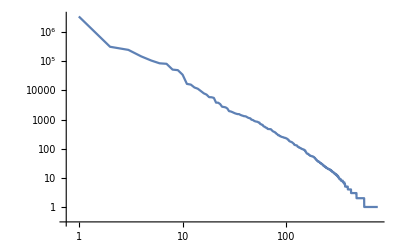

```mathematica
ListLogLogPlot[Map[#[[2]]&,storyVocAVecSelClassW[4,"voc-only"]["20231001-29"]],Joined->True]
```

クラスタリング前の分布の確認

すべてのクラス

```mathematica
(storyVocAVecSelClassPCAW[4,"voc-only"]["20231001-29"]=PrincipalComponents[N[Map[#[[1]]&,storyVocAVecSelClassW[4,"voc-only"]["20231001-29"]]]])//Dimensions
```

{759,59}

```mathematica
Graphics3D[Map[Point[#[[1;;3]]]&,storyVocAVecSelClassPCAW[4,"voc-only"]["20231001-29"]]]
```

-Graphics3D-

メンバーの多いクラス上位50

```mathematica
(storyVocAVecSelClassPCAW[4,"voc-only","top50"]["20231001-29"]=PrincipalComponents[N[Map[#[[1]]&,storyVocAVecSelClassW[4,"voc-only","top50"]["20231001-29"]]]])//Dimensions
```

{50,59}

```mathematica
Graphics3D[Map[Point[#[[1;;3]]]&,storyVocAVecSelClassPCAW[4,"voc-only","top50"]["20231001-29"]]]
```

-Graphics3D-

上位50クラスを階層クラスタリング

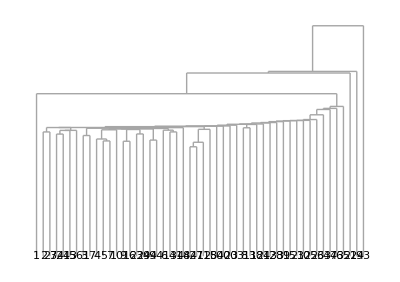

```mathematica
Dendrogram[storyVocAVecSelClassW[4,"voc-only","top50"]["20231001-29"]->Table[n,{n,50}]]
```

### 滞在・滞留時間データ

```mathematica
accTimeSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_accTime.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231009/T=4/_story/log-analysis_20231009_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231010/T=4/_story/log-analysis_20231010_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231011/T=4/_story/log-analysis_20231011_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231012/T=4/_story/log-analysis_20231012_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231013/T=4/_story/log-analysis_20231013_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231014/T=4/_story/log-analysis_20231014_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231015/T=4/_story/log-analysis_20231015_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231016/T=4/_story/log-analysis_20231016_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231017/T=4/_story/log-analysis_20231017_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231018/T=4/_story/log-analysis_20231018_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231019/T=4/_story/log-analysis_20231019_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231020/T=4/_story/log-analysis_20231020_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231021/T=4/_story/log-analysis_20231021_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231022/T=4/_story/log-analysis_20231022_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231023/T=4/_story/log-analysis_20231023_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231024/T=4/_story/log-analysis_20231024_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231025/T=4/_story/log-analysis_20231025_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231026/T=4/_story/log-analysis_20231026_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231027/T=4/_story/log-analysis_20231027_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231028/T=4/_story/log-analysis_20231028_accTime.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231029/T=4/_story/log-analysis_20231029_accTime.save}

```mathematica
start=Now
Map[Get,accTimeSaveFile];
end=Now
end-start
```

Wed 13 Mar 2024 11:14:32GMT+9

Wed 13 Mar 2024 11:16:00GMT+9

1.46262 min

```mathematica
(edgeAccTimeListW[4]["20231001-29"]=Apply[Join,Map[edgeAccTimeList[4,"stay"][fileDates[[#]]]&,tIDs]])//Dimensions
```

{4713453}

### 滞留時間

```mathematica
(edgeAccTimeListW[4,"stay"]["20231001-29"]=Apply[Join,Map[edgeAccTimeList[4,"stay"][fileDates[[#]]]&,tIDs]])//Dimensions
```

{4713453}

### ページ滞在時間（取得できないものは0としている）

```mathematica
(edgeAccTimeListW[4,"pagevisit"]["20231001-29"]=Apply[Join,Map[edgeAccTimeList[4,"pagevisit"][fileDates[[#]]]&,tIDs]])//Dimensions
```

{4713453}

## KirchhoffMatrix from voc graph

### キルヒホフ行列データ

```mathematica
KMSaveFile=Table[fileDirs[[tIDs[[n]]]]<>"/log-analysis_"<>fileDates[[tIDs[[n]]]]<>"_KM.save",{n,Length[tIDs]}]
```

{/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231002/T=4/_story/log-analysis_20231002_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231003/T=4/_story/log-analysis_20231003_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231004/T=4/_story/log-analysis_20231004_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231005/T=4/_story/log-analysis_20231005_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231006/T=4/_story/log-analysis_20231006_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231007/T=4/_story/log-analysis_20231007_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231009/T=4/_story/log-analysis_20231009_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231010/T=4/_story/log-analysis_20231010_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231011/T=4/_story/log-analysis_20231011_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231012/T=4/_story/log-analysis_20231012_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231013/T=4/_story/log-analysis_20231013_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231014/T=4/_story/log-analysis_20231014_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231015/T=4/_story/log-analysis_20231015_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231016/T=4/_story/log-analysis_20231016_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231017/T=4/_story/log-analysis_20231017_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231018/T=4/_story/log-analysis_20231018_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231019/T=4/_story/log-analysis_20231019_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231020/T=4/_story/log-analysis_20231020_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231021/T=4/_story/log-analysis_20231021_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231022/T=4/_story/log-analysis_20231022_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231023/T=4/_story/log-analysis_20231023_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231024/T=4/_story/log-analysis_20231024_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231025/T=4/_story/log-analysis_20231025_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231026/T=4/_story/log-analysis_20231026_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231027/T=4/_story/log-analysis_20231027_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231028/T=4/_story/log-analysis_20231028_KM.save,/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231029/T=4/_story/log-analysis_20231029_KM.save}

```mathematica
start=Now
Map[Get,KMSaveFile];
end=Now
end-start
```

Wed 13 Mar 2024 11:30:12GMT+9

Wed 13 Mar 2024 11:53:37GMT+9

23.4037 min

### キルヒホフ固有値によるクラスタリング

キルヒホフ行列の固有値列

```mathematica
(storyVocGraphEva59W[4]["20231001-29"]=Apply[Join,Map[storyVocGraphEva59[4][fileDates[[#]]]&,tIDs]])//Dimensions
```

{4713453,59}

Tallyでクラスをつくる

```mathematica
(storyVocGraphEva59CLassW[4]["20231001-29"]=Sort[Tally[storyVocGraphEva59W[4]["20231001-29"]],#1[[2]]>#2[[2]]&])//Dimensions
```

{19366,2}

クラスをExport

```mathematica
exportfileKM=basedir<>"storyVocAVecSelClassW_KM_20231001-29.txt"
```

/Volumes/home/NII/togo-log/rcoslogs/log/M=202310-202312/storyVocAVecSelClassW_KM_20231001-29.txt

```mathematica
(*Export[exportfileKM,FullForm[storyVocGraphEva59CLassW[4]["20231001-29"]],"String"]*)
```

```mathematica
(storyVocGraphEva59CLassW[4]["20231001-29","top50"]=storyVocGraphEva59CLassW[4]["20231001-29"][[1;;50]])//Dimensions
```

{50,2}

クラスのメンバー数確認

```mathematica
Map[#[[2]]&,storyVocGraphEva59CLassW[4]["20231001-29"]]//Total
```

4713453

```mathematica
Map[#[[2]]&,storyVocGraphEva59CLassW[4]["20231001-29","top50"]]//Total
```

4632131

キルヒホフ固有値でクラスを作った場合メンバー数上位50クラスで98%

```mathematica
4632131/4713453//N
```

0.982747

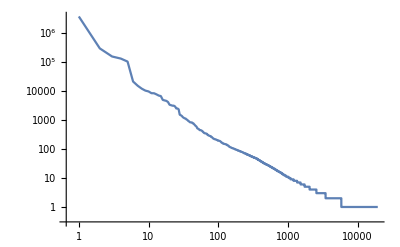

```mathematica
ListLogLogPlot[Map[#[[2]]&,storyVocGraphEva59CLassW[4]["20231001-29"]],Joined->True]
```

クラスタリング前の分布の確認

クラスの固有値列のPCA

```mathematica
Eva59ClassNum=(storyVocGraphEva59CLassPCAW[4]["20231001-29"]=PrincipalComponents[Map[#[[1]]&,storyVocGraphEva59CLassW[4]["20231001-29"]]])//Length
```

19366

```mathematica
Graphics3D[Map[Point[#[[1;;3]]]&,storyVocGraphEva59CLassPCAW[4]["20231001-29"]]]
```

-Graphics3D-

クラスtop50の固有値列のPCA

```mathematica
(storyVocGraphEva59CLassPCAW[4]["20231001-29","top50"]=PrincipalComponents[Map[#[[1]]&,storyVocGraphEva59CLassW[4]["20231001-29","top50"]]])//Dimensions
```

{50,59}

```mathematica
Graphics3D[Map[Point[#[[1;;3]]]&,storyVocGraphEva59CLassPCAW[4]["20231001-29","top50"]]]
```

-Graphics3D-

上位50クラスをクラスタリング

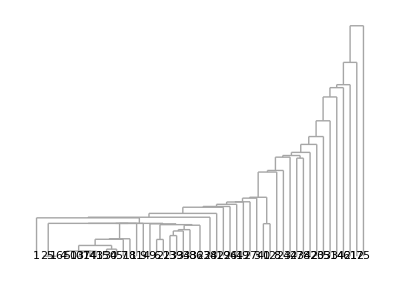

```mathematica
Dg=Dendrogram[   N[Map[#[[1]]&,storyVocGraphEva59CLassW[4]["20231001-29","top50"]]]   ->Table[n,{n,50}]   ]
```

## 変数

```mathematica
Names["Global`*"]
```

{a,accTimeSaveFile,a$,basedir,c,datadir,Dg,edgeAccTimeList,edgeAccTimeListW,end,Eva59ClassNum,EVSaveFile,fileDates,fileDirs,KMSaveFile,n,r,start,storyEdgeSel,storyEdgeSelW,storyNodeInOutClass,storyNodeInOutClassW,storyNodePSel,storyNodePSelW,storyNodeSel,storyNodeSelW,storyVocAVecSel,storyVocAVecSelClassPCAW,storyVocAVecSelClassW,storyVocAVecSelW,storyVocCVecSel,storyVocGraphEva59,storyVocGraphEva59CLassPCAW,storyVocGraphEva59CLassW,storyVocGraphEva59W,storyVocGraphKM59,submittext,tallysortW,tIDs,voc,vocDetailPos,vocDetailPosW,vocdir,vocNoDetailPosW,vocVecSaveFile,week,x,zipf,zipffitW}

## 分析方法

クラスのメンバーを確認する例

1 番目のクラス

```mathematica
storyVocAVecSelClassW[4,"voc-only"]["20231001-29"][[1]]
```

{{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},3420455}

のメンバーが元データのどのpositionか？

```mathematica
(pos=(Position[storyVocAVecSelW[4,"voc-only"]["20231001-29"],storyVocAVecSelClassW[4,"voc-only"]["20231001-29"][[1,1]]]))//Length
```

3420455